### χ^2 test from mock exam

{{1,Log[103]},{2,Log[80]},{3,Log[79]},{4,Log[71]},{5,Log[50]},{6,Log[52]},{7,Log[46]},{8,Log[51]}}

0.420599

1.41178

{{1,103},{2,80},{3,79},{4,71},{5,50},{6,52},{7,46},{8,51}}

24.2089

80.3834

{{1.,4.49919},{1.1,4.48419},{1.2,4.46919},{1.3,4.45419},{1.4,4.43919},{1.5,4.42419},{1.6,4.40919},{1.7,4.39419},{1.8,4.37919},{1.9,4.36419},{2.,4.34919},{2.1,4.33419},{2.2,4.31919},{2.3,4.30419},{2.4,4.28919},{2.5,4.27419},{2.6,4.25919},{2.7,4.24419},{2.8,4.22919},{2.9,4.21419},{3.,4.19919},{3.1,4.18419},{3.2,4.16919},{3.3,4.15419},{3.4,4.13919},{3.5,4.12419},{3.6,4.10919},{3.7,4.09419},{3.8,4.07919},{3.9,4.06419},{4.,4.04919},{4.1,4.03419},{4.2,4.01919},{4.3,4.00419},{4.4,3.98919},{4.5,3.97419},{4.6,3.95919},{4.7,3.94419},{4.8,3.92919},{4.9,3.91419},{5.,3.89919},{5.1,3.88419},{5.2,3.86919},{5.3,3.85419},{5.4,3.83919},{5.5,3.82419},{5.6,3.80919},{5.7,3.79419},{5.8,3.77919},{5.9,3.76419},{6.,3.74919},{6.1,3.73419},{6.2,3.71919},{6.3,3.70419},{6.4,3.68919},{6.5,3.67419},{6.6,3.65919},{6.7,3.64419},{6.8,3.62919},{6.9,3.61419},{7.,3.59919},{7.1,3.58419},{7.2,3.56919},{7.3,3.55419},{7.4,3.53919},{7.5,3.52419},{7.6,3.50919},{7.7,3.49419},{7.8,3.47919},{7.9,3.46419},{8.,3.44919}}

{{1.,4.45919},{1.1,4.44019},{1.2,4.42119},{1.3,4.40219},{1.4,4.38319},{1.5,4.36419},{1.6,4.34519},{1.7,4.32619},{1.8,4.30719},{1.9,4.28819},{2.,4.26919},{2.1,4.25019},{2.2,4.23119},{2.3,4.21219},{2.4,4.19319},{2.5,4.17419},{2.6,4.15519},{2.7,4.13619},{2.8,4.11719},{2.9,4.09819},{3.,4.07919},{3.1,4.06019},{3.2,4.04119},{3.3,4.02219},{3.4,4.00319},{3.5,3.98419},{3.6,3.96519},{3.7,3.94619},{3.8,3.92719},{3.9,3.90819},{4.,3.88919},{4.1,3.87019},{4.2,3.85119},{4.3,3.83219},{4.4,3.81319},{4.5,3.79419},{4.6,3.77519},{4.7,3.75619},{4.8,3.73719},{4.9,3.71819},{5.,3.69919},{5.1,3.68019},{5.2,3.66119},{5.3,3.64219},{5.4,3.62319},{5.5,3.60419},{5.6,3.58519},{5.7,3.56619},{5.8,3.54719},{5.9,3.52819},{6.,3.50919},{6.1,3.49019},{6.2,3.47119},{6.3,3.45219},{6.4,3.43319},{6.5,3.41419},{6.6,3.39519},{6.7,3.37619},{6.8,3.35719},{6.9,3.33819},{7.,3.31919},{7.1,3.30019},{7.2,3.28119},{7.3,3.26219},{7.4,3.24319},{7.5,3.22419},{7.6,3.20519},{7.7,3.18619},{7.8,3.16719},{7.9,3.14819},{8.,3.12919}}

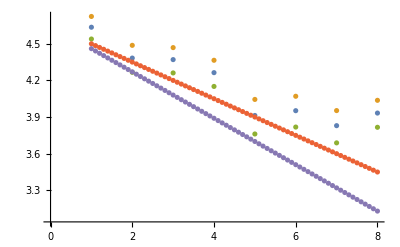

```mathematica
Subscript[N, 0]=104.5;
σ=1;
f1[x_]:=Log[Subscript[N, 0]] -0.15x;
f2[x_]:=Log[Subscript[N, 0]]-0.19x;
Data1=Log/@{{Exp[1],103},{Exp[2],80},{Exp[3],79},{Exp[4],71},{Exp[5],50},{Exp[6],52},{Exp[7],46},{Exp[8],51}};
Print[Data1];
Chis=((#[[2]]-f1[#[[1]]])^2/σ^2)&/@Data1;
Print[Total[Chis]];
Chis=((#[[2]]-f2[#[[1]]])^2/σ^2)&/@Data1;
Print[Total[Chis]];

f1[x_]:=Subscript[N, 0] Exp[-0.15x];
f2[x_]:=Subscript[N, 0] Exp[-0.19x];
Data={{1,103},{2,80},{3,79},{4,71},{5,50},{6,52},{7,46},{8,51}};
Print[Data];
Chis=((#[[2]]-f1[#[[1]]])^2/f1[#[[1]]])&/@Data;
Print[Total[Chis]];
Chis=((#[[2]]-f2[#[[1]]])^2/f2[#[[1]]])&/@Data;
Print[Total[Chis]];

NewData=({#[[1]],N[Log[#[[2]]]]})&/@Data;
UpperError=({#[[1]],N[Log[#[[2]]+Sqrt[f1[#[[1]]]]]]})&/@Data;
LowerError=({#[[1]],N[Log[#[[2]]-Sqrt[f1[#[[1]]]]]]})&/@Data;

f1Data=Table[{n,N[Log[f1[n]]]},{n,1,8,0.1}]
f2Data=Table[{n,N[Log[f2[n]]]},{n,1,8,0.1}]


pl=ListPlot[{NewData,UpperError,LowerError,f1Data,f2Data}];

Quit[];
```